# Additional 2D Constructions

Math 250 - Math with Mathematica
Christopher Hanusa

## 9.1 Overview

In this tutorial, we highlight additional ways to produce two-dimensional graphics.

## 9.2 Plotting functions of one variable (1D output)

When you want to plot the graph of a function, use the Plot command.  Use the PlotRange option to specify the range of possible values on the y-axis and the PlotStyle option to change the style of the curve.

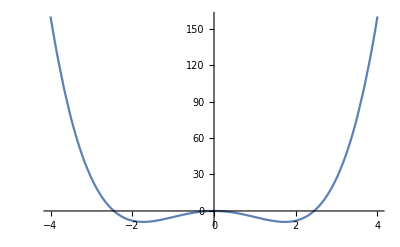
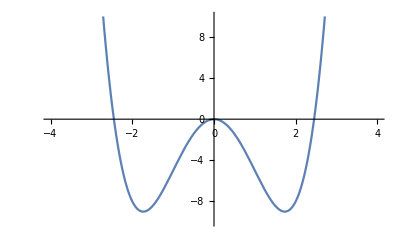
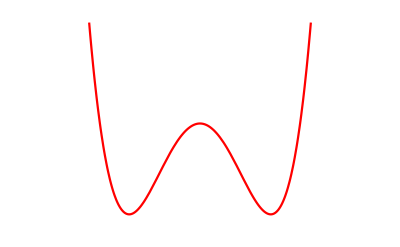

```mathematica
{
Plot[x^4-6x^2,{x,-4,4}],
Plot[x^4-6x^2,{x,-4,4},PlotRange->{-10,10}],
Plot[x^4-6x^2,{x,-4,4},PlotRange->{-10,10},PlotStyle->Red,Axes->False]
}
```

## 9.3 Plotting parametric curves (1D output)

Another type of curve is a parametric curve, where both the x-coordinate and y-coordinate are defined as a function of an independent variable.  For this type of curve, use ParametricPlot.

For example, the unit circle can be written as points of the form (cos(x),sin(x)) as x ranges from 0 to 2π.

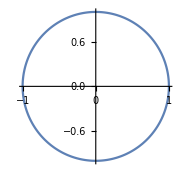

```mathematica
ParametricPlot[{Cos[x],Sin[x]},{x,0,2Pi}]
```

A fun modification of these functions gives Lissajous curves:

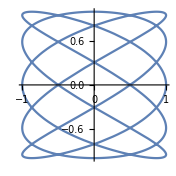

```mathematica
ParametricPlot[{Cos[5x],Sin[3x]},{x,0,2Pi}]
```

Here is a variety of graphs determined by various coefficients of x in the previous code.

```mathematica
TableForm[Table[ParametricPlot[{Cos[i x],Sin[j x]},{x,0,2Pi},ImageSize->100],{i,5},{j,5}]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### D’oh!

Parametric curves can create many sorts of shapes.  Here we have searched Mathematica for the “Homer Simpson curve”.
Expand the cell to see the code.

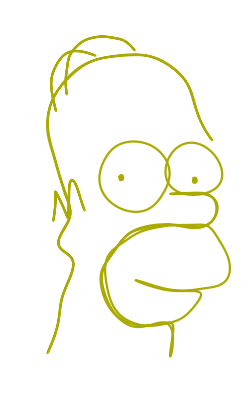

```mathematica
ParametricPlot[{{131.375-1.375 Sin[1.54545-8. t]-0.75 Sin[1.57143-6. t]-0.9 Sin[1.54545-5. t]+38.7778 Sin[1.57143+t]+1.41667 Sin[1.6+2. t]+7.02439 Sin[1.6+3. t]+6.9 Sin[1.6+4. t]+1.6 Sin[1.625+7. t]+0.571429 Sin[1.64706+9. t]+0.571429 Sin[1.72727+10. t],487.727-0.363636 Sin[1.4-10. t]-0.6875 Sin[1.07692-7. t]-43.7273 Sin[1.54545-4. t]-11.1429 Sin[1.52941-3. t]+19.9091 Sin[1.57143+t]+2.14286 Sin[1.63636+2. t]+6.27273 Sin[1.57143+5. t]+2.58333 Sin[4.7+6. t]+0.625 Sin[1.58333+8. t]+1.11111 Sin[1.54545+9. t]},{124.5-0.75 Sin[1.57143-5. t]-54. Sin[1.57143-1. t]+29.625 Sin[1.57143+2. t]+4.72727 Sin[4.71429+3. t]+4.22222 Sin[1.57143+4. t],872.952-5.76923 Sin[1.55556-4. t]-26.4 Sin[1.57143-2. t]-83. Sin[1.57143-1. t]+0.142857 Sin[4.7+3. t]+0.125 Sin[1.27273+5. t]},{201.571-1.77778 Sin[1.55556-5. t]-2.5 Sin[1.55556-3. t]+97.625 Sin[4.71429+t]+26.4545 Sin[1.57143+2. t]+3.28571 Sin[1.57143+4. t]+0.947368 Sin[1.57143+6. t]+0.4 Sin[4.69231+7. t]+1.04348 Sin[1.55556+8. t]+0.037037 Sin[0.454545+9. t]+0.363636 Sin[1.57143+10. t]+0.0133333 Sin[0.625+11. t],929.375+63.6667 Sin[4.71429+t]+40.4444 Sin[4.71429+2. t]+1.95455 Sin[4.66667+3. t]+7.52381 Sin[4.71429+4. t]+0.25 Sin[4.35294+5. t]+4.03333 Sin[4.7+6. t]+0.111111 Sin[2.83333+7. t]+2.27273 Sin[4.69231+8. t]+0.166667 Sin[4.44444+9. t]+1.16667 Sin[4.7+10. t]+0.0714286 Sin[1.96429+11. t]},{222.111-0.636364 Sin[1.3-13. t]+187.688 Sin[4.71429+t]+122.4 Sin[1.57143+2. t]+49.2727 Sin[4.7+3. t]+19.5714 Sin[4.63636+4. t]+7.57143 Sin[1.54545+5. t]+1.91667 Sin[4.55556+6. t]+8.54545 Sin[4.63636+7. t]+7.36364 Sin[4.55556+8. t]+4.41667 Sin[4.6+9. t]+3.47619 Sin[1.44444+10. t]+2.14286 Sin[1.2+11. t]+5.28571 Sin[1.4+12. t]+0.555556 Sin[3.85714+14. t]+5.14286 Sin[4.5+15. t]+2.95652 Sin[4.36364+16. t]+1.55556 Sin[4.57143+17. t],597.143-0.571429 Sin[1.55556-13. t]+354.875 Sin[4.7+t]+148.833 Sin[4.69231+2. t]+47.8182 Sin[1.6+3. t]+53.4667 Sin[4.7+4. t]+5.02778 Sin[4.33333+5. t]+24.0115 Sin[4.66667+6. t]+3.625 Sin[4.3125+7. t]+10.4167 Sin[4.7+8. t]+0.8 Sin[4.41667+9. t]+1.97872 Sin[4.69231+10. t]+0.3 Sin[1.28571+11. t]+2.6 Sin[4.66667+12. t]+1.95238 Sin[4.4+14. t]+0.8 Sin[4.4+15. t]+2.8 Sin[4.54545+16. t]+2.42857 Sin[4.44444+17. t]},{397.167+89.0526 Sin[1.52632+t]+104.4 Sin[1.45455+2. t]+63.9167 Sin[4.53846+3. t]+23.2727 Sin[4.42857+4. t]+20.2 Sin[4.36364+5. t]+20.375 Sin[4.3+6. t]+6.72727 Sin[4.08333+7. t]+8.75 Sin[4.1+8. t]+1.46667 Sin[2.07143+9. t]+4.3 Sin[4.+10. t]+2.28571 Sin[1.2+11. t]+0.52381 Sin[3.92857+12. t]+0.75 Sin[3.7+13. t]+1.3 Sin[3.85714+14. t],305.024-1.75 Sin[0.727273-14. t]-2.84615 Sin[1.5-12. t]+250.182 Sin[1.52381+t]+27.4783 Sin[4.66667+2. t]+4.83333 Sin[1.47619+3. t]+22.2727 Sin[1.25+4. t]+12.0625 Sin[1.4+5. t]+9.5 Sin[4.57143+6. t]+3.8 Sin[1.88889+7. t]+14.5217 Sin[4.375+8. t]+3.66667 Sin[1.90909+9. t]+7.06667 Sin[4.4+10. t]+3.46667 Sin[1.58333+11. t]+3.5 Sin[1.23077+13. t]},{295.25-0.111111 Sin[1.4-10. t]-0.222222 Sin[1.22222-6. t]+1.81818 Sin[1.06667+t]+0.538462 Sin[3.75+2. t]+4.30769 Sin[2.77778+3. t]+0.166667 Sin[3.73333+4. t]+0.3125 Sin[2.375+5. t]+0.4 Sin[0.3125+7. t]+0.416667 Sin[3.4+8. t]+0.25 Sin[3.+9. t],557.417-0.428571 Sin[0.1-9. t]-0.125 Sin[0.357143-5. t]-1.125 Sin[1.52941-2. t]+2.57143 Sin[1.27273+t]+4.98 Sin[4.625+3. t]+0.230769 Sin[2.11111+4. t]+0.4 Sin[4.0625+6. t]+0.529412 Sin[0.25+7. t]+0.3125 Sin[3.38462+8. t]+0.222222 Sin[2.9+10. t]},{517.125-0.166667 Sin[0.727273-5. t]+0.625 Sin[1.2+t]+2.6 Sin[3.21429+2. t]+3.33333 Sin[3.5+3. t]+1.3 Sin[0.96+4. t]+0.166667 Sin[1.8+6. t]+0.25 Sin[2.84615+7. t]+0.125 Sin[3.25+8. t]+0.111111 Sin[0.777778+9. t]+0.222222 Sin[2.52+10. t]+0.1 Sin[0.111111+11. t],549.286-0.037037 Sin[1.-11. t]-0.166667 Sin[0.363636-10. t]-0.2 Sin[0.181818-9. t]-0.35 Sin[0.5-5. t]-3.64286 Sin[1.03571-3. t]+3.28571 Sin[3.6+t]+2.77778 Sin[4.41667+2. t]+1.5 Sin[2.73333+4. t]+0.2 Sin[3.27273+6. t]+0.0833333 Sin[4.66667+7. t]+0.3 Sin[2.11111+8. t]},{432.25-1.30769 Sin[1.2-12. t]-2.14286 Sin[0.961538-11. t]-1.85714 Sin[0.214286-10. t]-3.57143 Sin[0.692308-6. t]-109.667 Sin[0.470588-1. t]+108.875 Sin[2.+2. t]+36.6429 Sin[1.25+3. t]+12.2222 Sin[0.375+4. t]+5.375 Sin[0.2+5. t]+3.30769 Sin[3.81818+7. t]+3.0625 Sin[0.846154+8. t]+2.2 Sin[0.285714+9. t]+0.714286 Sin[3.23077+13. t],261.8-1.14286 Sin[0.333333-13. t]-0.692308 Sin[0.8-11. t]-1.68421 Sin[1.41667-9. t]-1.83333 Sin[0.692308-8. t]-11.2667 Sin[0.470588-3. t]+114.625 Sin[4.58333+t]+66.9 Sin[0.307692+2. t]+11.0909 Sin[2.04167+4. t]+3.44444 Sin[0.125+5. t]+2.77778 Sin[0.857143+6. t]+4.3 Sin[0.047619+7. t]+0.947368 Sin[0.692308+10. t]+0.222222 Sin[2.06667+12. t]},{514.182+85.4 Sin[2.02222+t]+0.272727 Sin[3.5+2. t],577.357-7.02632 Sin[0.3-2. t]+78.125 Sin[3.64706+t]},{336.364-1.11111 Sin[0.7-4. t]-0.538462 Sin[0.833333-3. t]-104.571 Sin[0.571429-1. t]+2.03226 Sin[0.0212766+2. t]+1.6875 Sin[2.75+5. t],562.75+105.385 Sin[4.16667+t]+1.95238 Sin[4.01961+2. t]+0.6875 Sin[0.615385+3. t]+0.692308 Sin[2.88889+4. t]+1.2 Sin[0.785714+5. t]}},{t,0,2 π},Axes->False,PlotStyle->Darker[Yellow]]
```

## 9.4 Splines (1D output)

Plot and ParametricPlot require that you already know the function.  If you instead have points that you would like to serve as a guide for a smooth curve, use the BSplineCurve command. The output is a graphics primitive.

```mathematica
?BSplineCurve
```

BSplineCurve[{pt_1,pt_2,…}] is a graphics primitive that represents a nonuniform rational B-spline curve with control points pt_i.

```mathematica
pts={{0,0},{1,2},{2,0},{3,2},{4,2},{5,1}};
```

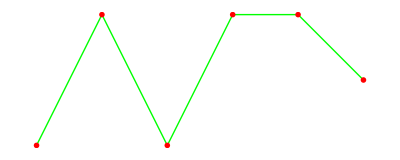

```mathematica
Graphics[{Green,Line[pts],PointSize[.01],Red,Point[pts]}]
```

```mathematica
Graphics[{BSplineCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

-Graphics-

You can use the SplineClosed option to close up the curve in a smooth fashion.

```mathematica
Graphics[{BSplineCurve[pts,SplineClosed->True],Green,Line[Append[pts,pts[[1]]]],Red,Point[pts]}]
```

-Graphics-

The Documentation Center entry for BSplineCurve has an example explaining how to ensure that your spline passes through the given points.  Another option is the command Interpolation.

## 9.5 Creating a region with a spline boundary (2D output)

When we replace the BSplineCurve command with a BSplineFunction command, the curve becomes a parametrically defined function. As a consequence, you can use ParametricPlot to graph the curve again using a dummy variable ranging from zero to one. This will be a useful technique that we’ll apply in 3D too.

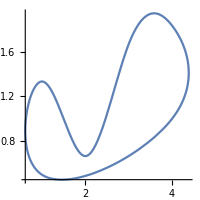

```mathematica
curve=ParametricPlot[BSplineFunction[pts,SplineClosed->True][t],{t,0,1},ImageSize->200]
```

The BoundaryDiscretizeGraphics command converts the closed curve into a BoundaryMeshRegion. (This is good!  We’ll learn about it in a later tutorial.)

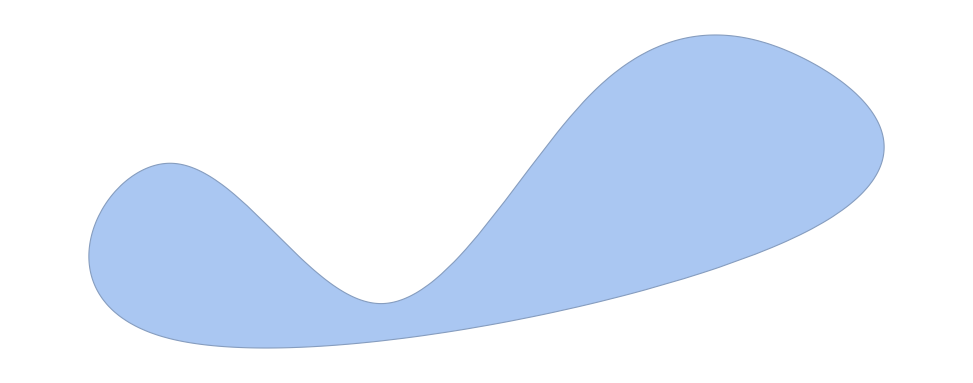

```mathematica
shape=BoundaryDiscretizeGraphics[curve]
```

In Mathematica Version 12 and later, such a two-dimensional region can be used in Graphics just like a Polygon can.

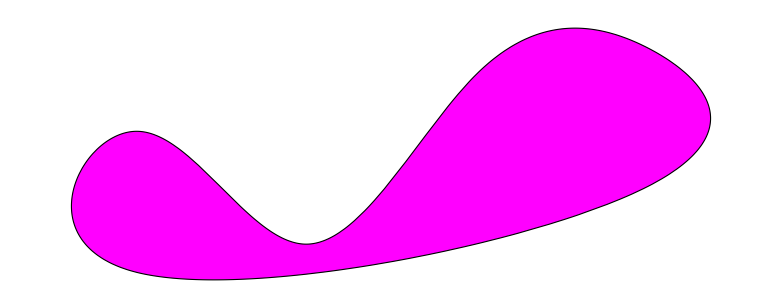

```mathematica
Graphics[{EdgeForm[{Black,Thick}],Magenta,shape},ImageSize->200]
```

## 9.6 RegionPlot (2D output)

Another way to plot a closed region in 2D space is to use RegionPlot.  It produces gives all the points in the specified region that satisfy your given requirements.

```mathematica
?RegionPlot
```

RegionPlot[pred,{x,x_min,x_max},{y,y_min,y_max}] makes a plot showing the region in which pred is True.

To make a disk, you can specify that you want all points within distance 1 from the origin:

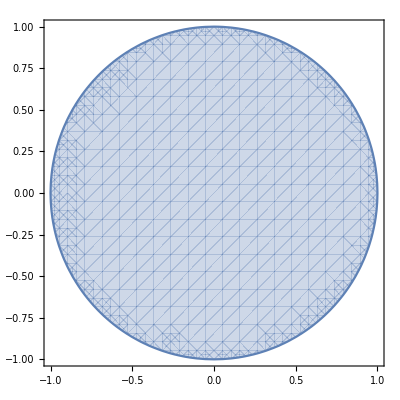

```mathematica
RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]
```

Use the And (&&) and Or (||) operators to do operations on regions.  For example, consider the two constraints:

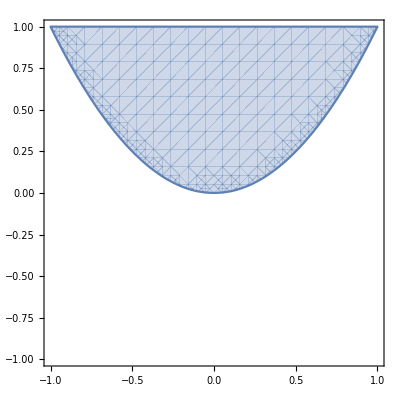
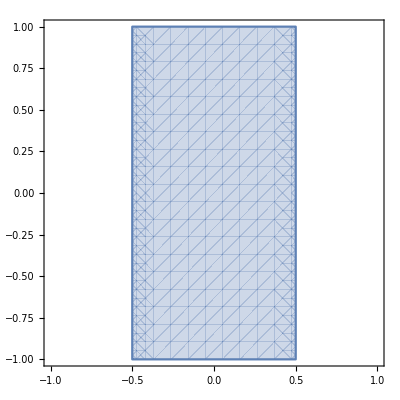

```mathematica
{RegionPlot[y≥x^2,{x,-1,1},{y,-1,1}],RegionPlot[-.5≤x≤.5,{x,-1,1},{y,-1,1}]}
```

Use And to create the intersection of the regions and use Or to create the union of the regions.

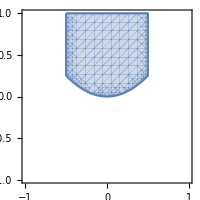

```mathematica
RegionPlot[y≥x^2&&-.5≤x≤.5,{x,-1,1},{y,-1,1},ImageSize->200]
```

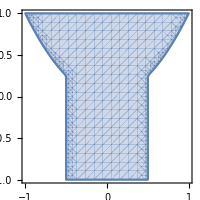

```mathematica
RegionPlot[y≥x^2||-.5≤x≤.5,{x,-1,1},{y,-1,1},ImageSize->200]
```